## Compute k

```mathematica
gamma1 = 4.13;
gamma2 = 8.43;
l1=0.9;
l2 =0.95;
Ceiling[gamma1/(1-l1)-1]
Ceiling[gamma1/(1-l2)-1]
Ceiling[gamma2-1+Sqrt[-Log[1-l1]*2(gamma2+1)^2]]
Ceiling[gamma2-1+Sqrt[-Log[1-l2]*2(gamma2+1)^2]]
```

## Plot Trajectories

### circuit

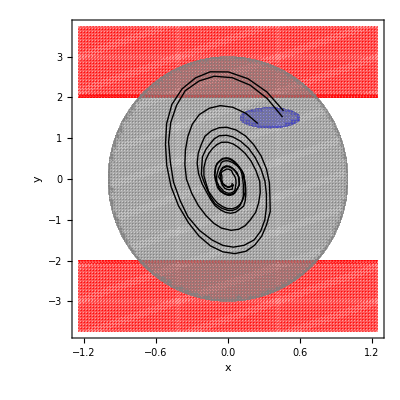

```mathematica
varSet = {x, y};
varRange = {{-1.25,1.25},{-3.75,3.75}}; 
flowVec = {8/9*x-1/18*y, x+y}; 
flowDist [x_]:={8/9*x[[1]]-1/18*x[[2]]+0.01*RandomVariate[UniformDistribution[{-1,1}]],x[[1]]+x[[2]]} 
(*+d for disturbance, uniform distribution [-1,1]*)
unsafeBoundary = {4-y^2};
initBoundary = {(x-0.35)^2+(y-1.5)^2-0.25^2};
domainBoundary = {9x^2+y^2-3^2};
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];

flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];

initCons=And@@Thread[LessEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[LessEqualThan[0][unsafeBoundary]];
domainCons=And@@Thread[LessEqualThan[0][domainBoundary]];

initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.4], Blue},BoundaryStyle->None ,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Red},BoundaryStyle->None,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
domainPlot=RegionPlot[domainCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Gray},BoundaryStyle->None,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
initSamples = RandomPoint[ImplicitRegion[initCons,{x,y}],3];
trajGen[x_]:= NestList[flowDist,x,100];
trajTable = Map[trajGen,initSamples];
trajPlot = ListLinePlot[trajTable,PlotStyle->Directive[Black,Thickness[Medium]]];
Show[initPlot,unsafePlot,domainPlot,trajPlot,FrameLabel->{x,y}]
```

### vanderpol

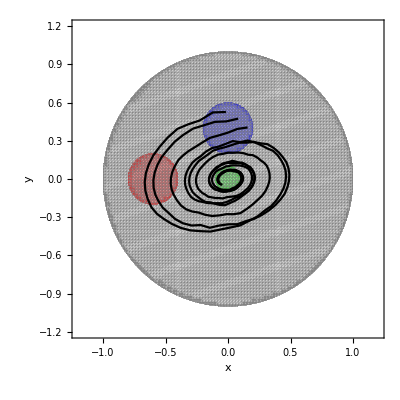

```mathematica
varSet = {x, y};
varRange = {{-1.2,1.2},{-1.2,1.2}}; 
flowVec = {-2*y, x+0.5*(x^2-1)*y}; 
flowDist [x_]:={x[[1]]-0.1*2*x[[2]], x[[2]]+0.1*(x[[1]]+0.5*(x[[1]]^2-1-RandomVariate[UniformDistribution[{-1,1}]])*x[[2]])} ;

(*+d for disturbance, uniform distribution [-1,1]*)
initBoundary = {x^2+(y-0.4)^2-0.2^2};
unsafeBoundary = {(x+0.6)^2+y^2-0.2^2};
targetBoundary = {x^2+y^2-0.1^2};
domainBoundary = {x^2+y^2-1^2};

ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];

flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];

initCons=And@@Thread[LessEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[LessEqualThan[0][unsafeBoundary]];
targetCons=And@@Thread[LessEqualThan[0][targetBoundary]];
domainCons=And@@Thread[LessEqualThan[0][domainBoundary]];

initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[0.4], Blue},BoundaryStyle->None ,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Red},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
targetPlot=RegionPlot[targetCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Green},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
domainPlot=RegionPlot[domainCons,Evaluate[ranges],PlotStyle->{Opacity[0.4],Gray},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
initSamples = RandomPoint[ImplicitRegion[initCons,{x,y}],3];
trajGen[x_]:= NestList[flowDist,x,150];
trajTable = Map[trajGen,initSamples];
trajPlot = ListLinePlot[trajTable,PlotStyle->Directive[Black,Thickness[Medium]]];
Show[initPlot,unsafePlot,targetPlot,domainPlot,trajPlot,FrameLabel->{x,y}]
```

### randomwalk

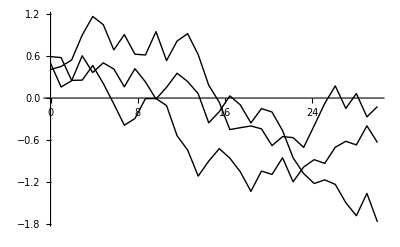

```mathematica
flowDist [x_]:=If[-2≤ x&&x≤ 2,x+0.4*RandomVariate[UniformDistribution[{-1.1,0.9}]],x];

initSamples = Flatten[RandomPoint[ImplicitRegion[0.4≤ x≤ 0.6,{x}],3]];
trajGen[x_]:= NestList[flowDist,x,31];
trajTable = Map[trajGen,initSamples];
trajPlot = ListLinePlot[trajTable,DataRange->{0,30},PlotStyle->Directive[Black,Thickness[Medium]]];
Show[trajPlot]
```

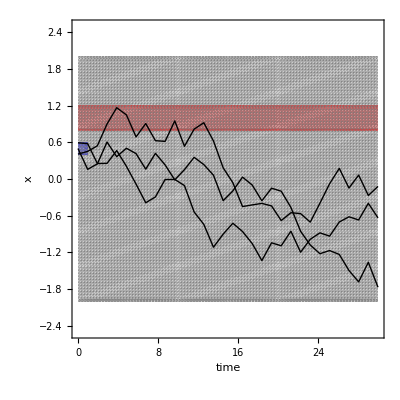

```mathematica
initPlot=RegionPlot[0≤ x&&x≤1&&0.4≤ y≤ 0.6,{x,0,30},{y,-2.5,2.5},PlotStyle->{Opacity[0.4], Blue},BoundaryStyle->None ,PlotPoints-> 100];
unsafePlot=RegionPlot[0≤ x&&x≤ 30&&0.8≤ y&&y≤ 1.2,{x,0,30},{y,-2.5,2.5},PlotStyle->{Opacity[0.4],Red},BoundaryStyle->None,PlotPoints-> 100];
domainPlot=RegionPlot[-2≤ y≤ 2,{x,0,30},{y,-2.5,2.5},PlotStyle->{Opacity[0.4],Gray},BoundaryStyle->None,PlotPoints-> 100];
Show[initPlot,unsafePlot,domainPlot,trajPlot,FrameLabel->{time,x}]
```